```mathematica
(*Name:Tommy Lee Truong
Last Edit: Nov 21 2016
Program Name: Assignment 2*)
```

# Assignment 2

The wavefunctions for a 1-dimensional particle-in-a-box (PIB) have the functional form Ψ(x)=√(2/L)sin((n π)/L x), where n is an integer greater than zero and L is the length of the box. Write a function, called psiTrue, that returns the value of the first (i.e. n=1) wavefunction, for a box with a length of 1, and plot the function from 0 to 1.

```mathematica
Ψ[x_,L_,n_]:=(√(2/L))*(Sin[(n*π*x)/L])
```

```mathematica
Ψ[x,1,1]
```

√2 Sin[π x]

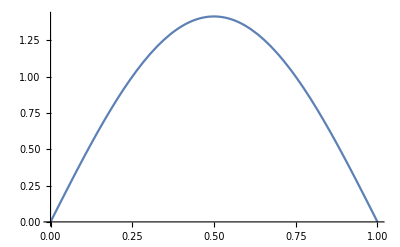

```mathematica
Plot[{Ψ[x,1,1]},{x,0,1}]
```

An important attribute for wavefunctions is that the are normalized (or at least normalizable). The interpretation of a normalized wavefunction is that the probibility of finding the particle somewhere is equal to 1. The mathematical meaning behind this is that the integral over all space of the wavefunction squared is equal to 1. For us, this means that the integral of psiTrue^2 from zero to one is equal to one. Show that psiTrue is normalized.

```mathematica
[(∫_0^1 Ψ[x,1,1]ⅆx)^2]
```

{}

```mathematica
NSolve[F[x]]
```

{{x→ConditionalExpression[0.31831 (0.+6.28319 C[1]),C[1]∈Integers]}}

Once we know the wavefunction for a quantum mechanical object, it turns out we know everything we can possibly know about that object. For example, we can calculate it’s average position, as well as it’s average energy. To calculate properties (called “observables” in quantum mechanics) from a wavefunction, we first need mathematical functions that are called operators. For example, the position operator is “multiply by x”, while the energy operator in this model is “take the second derivative, and multiply by -h/(8π m), where h is Planck’s constant and m is the object’s mass”. Once we have found the operator of interest, we calculate the property by integrating over all space (from 0 to 1 for this problem) the wavefunction times the operator times the wavefunction. Calculate the average position and average energy for the wavefunction psiTrue. Do these quantities make sense, or at least match the book?

An important theory in quantum mechanics is the variational theory. The variational theory tells us that if we don’t know the correct wavefunction for a quantum mechanical object, we can use another wavefunction, and the energy we calculate will always be larger than the true energy, and the closer the calculated energy is to the true energy, the better the test wavefunction approximates the true wavefunction. Create a function, called testPsi, with the formula √630 x^2 (1-x)^2, and show that this wavefunction is normalized.

Create a plot comparing the true wavefunction with the test wavefunction.

Calculate the average position and average energy of a particle with the test wavefunction.

Calculate the ratio of the average energy from the test wavefunction to the average energy of the true wavefunction. Does this ratio follow what we expect based on the variational theory?